# Omicron analysis: Plotting partitioned case counts and Rt

## Splitting out lineage BA.1 / clade 21K from lineage BA.2 / clade 21L

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries-split

```mathematica
dataset="omicron-countries-split";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
gridCount=4;
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron 21K","Omicron 21L"};
```

```mathematica
n=Length[variants]
```

4

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.7,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8083415999999999, 0.7110806000000001, 0.255976],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

### Countries

```mathematica
countriesToDrop={"Czech Republic"};
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-02-14

```mathematica
countries=Union[seqData[[All,2]]]
```

{Australia,Austria,Belgium,Canada,Czech Republic,Denmark,France,Germany,India,Indonesia,Ireland,Israel,Italy,Japan,Netherlands,New Zealand,Norway,Poland,Portugal,Romania,Singapore,South Africa,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
countries=Complement[countries,countriesToDrop]
```

{Australia,Austria,Belgium,Canada,Denmark,France,Germany,India,Indonesia,Ireland,Israel,Italy,Japan,Netherlands,New Zealand,Norway,Poland,Portugal,Romania,Singapore,South Africa,Spain,Sweden,Switzerland,Thailand,United Kingdom,USA}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->countrySequenceCounts[#][[-15;;-1]]&,countries]
```

{Australia→{{2022-01-31,175},{2022-02-01,214},{2022-02-02,169},{2022-02-03,147},{2022-02-04,112},{2022-02-05,73},{2022-02-06,111},{2022-02-07,47},{2022-02-08,114},{2022-02-09,35},{2022-02-10,46},{2022-02-11,37},{2022-02-12,17},{2022-02-13,23},{2022-02-14,18}},Austria→{{2022-01-31,5},{2022-02-01,23},{2022-02-02,84},{2022-02-03,251},{2022-02-04,115},{2022-02-05,0},{2022-02-06,0},{2022-02-07,0},{2022-02-08,15},{2022-02-09,139},{2022-02-10,125},{2022-02-11,88},{2022-02-12,0},{2022-02-13,0},{2022-02-14,0}},Belgium→{{2022-01-31,274},{2022-02-01,168},{2022-02-02,286},{2022-02-03,344},{2022-02-04,342},{2022-02-05,180},{2022-02-06,86},{2022-02-07,270},{2022-02-08,174},{2022-02-09,205},{2022-02-10,224},{2022-02-11,185},{2022-02-12,61},{2022-02-13,0},{2022-02-14,0}},Canada→{{2022-01-31,105},{2022-02-01,77},{2022-02-02,50},{2022-02-03,54},{2022-02-04,37},{2022-02-05,14},{2022-02-06,22},{2022-02-07,5},{2022-02-08,5},{2022-02-09,5},{2022-02-10,8},{2022-02-11,0},{2022-02-12,1},{2022-02-13,0},{2022-02-14,0}},Denmark→{{2022-01-31,2568},{2022-02-01,651},{2022-02-02,778},{2022-02-03,1429},{2022-02-04,1733},{2022-02-05,1913},{2022-02-06,1410},{2022-02-07,1529},{2022-02-08,1617},{2022-02-09,1160},{2022-02-10,1104},{2022-02-11,1555},{2022-02-12,1477},{2022-02-13,1551},{2022-02-14,295}},France→{{2022-01-31,2935},{2022-02-01,224},{2022-02-02,238},{2022-02-03,166},{2022-02-04,102},{2022-02-05,84},{2022-02-06,136},{2022-02-07,1888},{2022-02-08,160},{2022-02-09,91},{2022-02-10,96},{2022-02-11,46},{2022-02-12,32},{2022-02-13,0},{2022-02-14,0}},Germany→{{2022-01-31,1998},{2022-02-01,2314},{2022-02-02,1884},{2022-02-03,2101},{2022-02-04,1639},{2022-02-05,577},{2022-02-06,159},{2022-02-07,718},{2022-02-08,953},{2022-02-09,242},{2022-02-10,131},{2022-02-11,180},{2022-02-12,0},{2022-02-13,0},{2022-02-14,0}},India→{{2022-01-31,168},{2022-02-01,148},{2022-02-02,250},{2022-02-03,276},{2022-02-04,179},{2022-02-05,156},{2022-02-06,99},{2022-02-07,124},{2022-02-08,108},{2022-02-09,2},{2022-02-10,28},{2022-02-11,16},{2022-02-12,12},{2022-02-13,0},{2022-02-14,0}},Indonesia→{{2022-01-31,42},{2022-02-01,35},{2022-02-02,82},{2022-02-03,69},{2022-02-04,43},{2022-02-05,31},{2022-02-06,11},{2022-02-07,12},{2022-02-08,9},{2022-02-09,1},{2022-02-10,4},{2022-02-11,4},{2022-02-12,4},{2022-02-13,0},{2022-02-14,0}},Ireland→{{2022-01-31,31},{2022-02-01,30},{2022-02-02,30},{2022-02-03,29},{2022-02-04,22},{2022-02-05,23},{2022-02-06,30},{2022-02-07,30},{2022-02-08,29},{2022-02-09,0},{2022-02-10,0},{2022-02-11,0},{2022-02-12,0},{2022-02-13,0},{2022-02-14,0}},Israel→{{2022-01-31,262},{2022-02-01,64},{2022-02-02,11},{2022-02-03,320},{2022-02-04,508},{2022-02-05,23},{2022-02-06,71},{2022-02-07,289},{2022-02-08,164},{2022-02-09,0},{2022-02-10,0},{2022-02-11,0},{2022-02-12,0},{2022-02-13,0},{2022-02-14,0}},Italy→{{2022-01-31,1031},{2022-02-01,162},{2022-02-02,75},{2022-02-03,45},{2022-02-04,106},{2022-02-05,62},{2022-02-06,47},{2022-02-07,67},{2022-02-08,26},{2022-02-09,21},{2022-02-10,35},{2022-02-11,14},{2022-02-12,45},{2022-02-13,0},{2022-02-14,0}},Japan→{{2022-01-31,6},{2022-02-01,1},{2022-02-02,2},{2022-02-03,5},{2022-02-04,3},{2022-02-05,3},{2022-02-06,2},{2022-02-07,5},{2022-02-08,3},{2022-02-09,3},{2022-02-10,0},{2022-02-11,18},{2022-02-12,4},{2022-02-13,0},{2022-02-14,0}},Netherlands→{{2022-01-31,191},{2022-02-01,171},{2022-02-02,144},{2022-02-03,98},{2022-02-04,121},{2022-02-05,67},{2022-02-06,38},{2022-02-07,36},{2022-02-08,26},{2022-02-09,17},{2022-02-10,13},{2022-02-11,16},{2022-02-12,10},{2022-02-13,0},{2022-02-14,0}},New Zealand→{{2022-01-31,17},{2022-02-01,6},{2022-02-02,24},{2022-02-03,4},{2022-02-04,1},{2022-02-05,1},{2022-02-06,0},{2022-02-07,0},{2022-02-08,0},{2022-02-09,0},{2022-02-10,0},{2022-02-11,0},{2022-02-12,0},{2022-02-13,0},{2022-02-14,0}},Norway→{{2022-01-31,98},{2022-02-01,140},{2022-02-02,42},{2022-02-03,33},{2022-02-04,17},{2022-02-05,9},{2022-02-06,98},{2022-02-07,12},{2022-02-08,12},{2022-02-09,10},{2022-02-10,13},{2022-02-11,13},{2022-02-12,4},{2022-02-13,0},{2022-02-14,0}},Poland→{{2022-01-31,849},{2022-02-01,576},{2022-02-02,576},{2022-02-03,360},{2022-02-04,354},{2022-02-05,201},{2022-02-06,126},{2022-02-07,358},{2022-02-08,243},{2022-02-09,26},{2022-02-10,168},{2022-02-11,14},{2022-02-12,65},{2022-02-13,0},{2022-02-14,0}},Portugal→{{2022-01-31,216},{2022-02-01,118},{2022-02-02,6},{2022-02-03,9},{2022-02-04,1},{2022-02-05,7},{2022-02-06,144},{2022-02-07,229},{2022-02-08,125},{2022-02-09,0},{2022-02-10,0},{2022-02-11,0},{2022-02-12,0},{2022-02-13,0},{2022-02-14,0}},Romania→{{2022-01-31,47},{2022-02-01,270},{2022-02-02,26},{2022-02-03,22},{2022-02-04,0},{2022-02-05,0},{2022-02-06,0},{2022-02-07,0},{2022-02-08,0},{2022-02-09,0},{2022-02-10,0},{2022-02-11,0},{2022-02-12,0},{2022-02-13,0},{2022-02-14,0}},Singapore→{{2022-01-31,27},{2022-02-01,25},{2022-02-02,26},{2022-02-03,37},{2022-02-04,31},{2022-02-05,35},{2022-02-06,38},{2022-02-07,23},{2022-02-08,33},{2022-02-09,51},{2022-02-10,26},{2022-02-11,34},{2022-02-12,27},{2022-02-13,0},{2022-02-14,0}},South Africa→{{2022-01-31,6},{2022-02-01,7},{2022-02-02,5},{2022-02-03,13},{2022-02-04,6},{2022-02-05,0},{2022-02-06,1},{2022-02-07,0},{2022-02-08,0},{2022-02-09,0},{2022-02-10,0},{2022-02-11,0},{2022-02-12,0},{2022-02-13,0},{2022-02-14,0}},Spain→{{2022-01-31,166},{2022-02-01,168},{2022-02-02,228},{2022-02-03,147},{2022-02-04,170},{2022-02-05,34},{2022-02-06,22},{2022-02-07,115},{2022-02-08,113},{2022-02-09,138},{2022-02-10,74},{2022-02-11,38},{2022-02-12,14},{2022-02-13,0},{2022-02-14,0}},Sweden→{{2022-01-31,389},{2022-02-01,203},{2022-02-02,295},{2022-02-03,119},{2022-02-04,83},{2022-02-05,58},{2022-02-06,108},{2022-02-07,357},{2022-02-08,215},{2022-02-09,90},{2022-02-10,48},{2022-02-11,21},{2022-02-12,2},{2022-02-13,0},{2022-02-14,0}},Switzerland→{{2022-01-31,602},{2022-02-01,232},{2022-02-02,347},{2022-02-03,107},{2022-02-04,109},{2022-02-05,81},{2022-02-06,178},{2022-02-07,349},{2022-02-08,194},{2022-02-09,59},{2022-02-10,17},{2022-02-11,17},{2022-02-12,8},{2022-02-13,0},{2022-02-14,0}},Thailand→{{2022-01-31,11},{2022-02-01,50},{2022-02-02,31},{2022-02-03,171},{2022-02-04,112},{2022-02-05,61},{2022-02-06,7},{2022-02-07,4},{2022-02-08,0},{2022-02-09,1},{2022-02-10,0},{2022-02-11,0},{2022-02-12,0},{2022-02-13,0},{2022-02-14,0}},United Kingdom→{{2022-01-31,9261},{2022-02-01,5149},{2022-02-02,9318},{2022-02-03,8239},{2022-02-04,6263},{2022-02-05,8109},{2022-02-06,7071},{2022-02-07,8378},{2022-02-08,8341},{2022-02-09,6476},{2022-02-10,6393},{2022-02-11,6740},{2022-02-12,4305},{2022-02-13,1918},{2022-02-14,1700}},USA→{{2022-01-31,6177},{2022-02-01,5862},{2022-02-02,6035},{2022-02-03,4594},{2022-02-04,4205},{2022-02-05,2126},{2022-02-06,2465},{2022-02-07,4783},{2022-02-08,3067},{2022-02-09,1739},{2022-02-10,732},{2022-02-11,534},{2022-02-12,136},{2022-02-13,0},{2022-02-14,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.00001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[4]]],PlotRange->{logitTransform[0.0005],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[4]]],PlotRange->{0,If[maxFreq>0.95,1,maxFreq]},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[country_]:=Map[logisticPrevSeries[countryVariantCounts[country,#],countrySequenceCounts[country]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForCountries=Map[freqForCountry,countries];
```

```mathematica
modeledFreqsForCountries=Map[{modeledLogisticPrevSeries[logisticPrevSeries[countryVariantCounts[#,"Omicron 21L"],countrySequenceCounts[#]]]}&,countries];
```

```mathematica
legendsForCountries=Map[constructGrowthRateLegend[modeledGrowthRate[#[[4]]],variants[[4]],legendStartingPointY- 0.09,colors[[4]]]&,freqsForCountries];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForCountries,modeledFreqsForCountries,legendsForCountries,countries}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

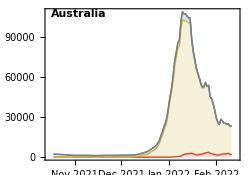
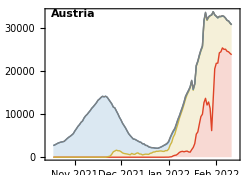
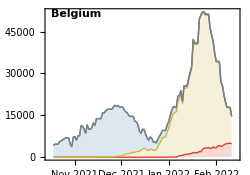
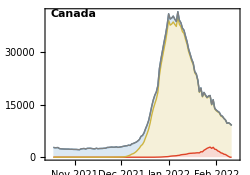
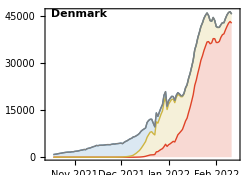
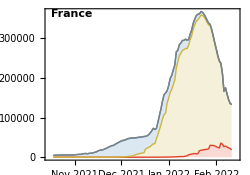
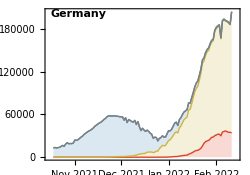
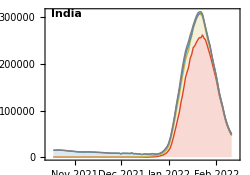
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=500000;
```

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[country_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{startDate,endDate},
{50,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[country_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[country,"Omicron 21L"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{startDate,endDate},
{50,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[4]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.88,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForCountries=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron 21L"]],"Omicron 21L",legendStartingPointY- 0.09,colors[[4]]]&,countries];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{countries,legendsForCountries}];
```

```mathematica
fig=Grid[gappedPartition[Join[Join[{legendPanel},Table[SpanFromLeft,{gridCount-1}]],panels],gridCount],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries-split_partitioned-log-cases.png